```mathematica
(*A + B*)
f[x_] =Sin[x^2]/x^2


y= Simplify[NSolve[{f[x] == 0 && x<2π && x>0}, x]]
```

Sin[x^2]/x^2

{{x→1.77245},{x→2.50663},{x→3.06998},{x→3.54491},{x→3.96333},{x→4.34161},{x→4.68947},{x→5.01326},{x→5.31736},{x→5.60499},{x→5.87856},{x→6.13996}}

{1.77245,2.50663,3.06998,3.54491,3.96333,4.34161,4.68947,5.01326,5.31736,5.60499,5.87856,6.13996}

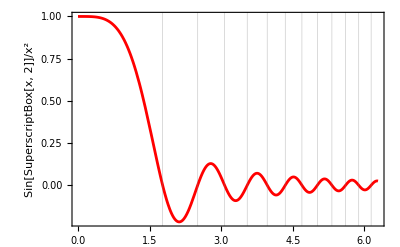

```mathematica
listOfAnswers=x/. y

Plot[Sin[x^2]/x^2,{x,0,2 π},PlotStyle->Red,Frame->True, FrameLabel->{{"Sin[SuperscriptBox[x, 2]]/x^2",None},{None,"0 < x < 2π"}}, GridLines->{listOfAnswers,None}]
```